```mathematica
ClearAll["Global`*"]
LaunchKernels[6]
```

{Local (6),Local (6),Local (6),Local (6),Local (6),Local (6)}

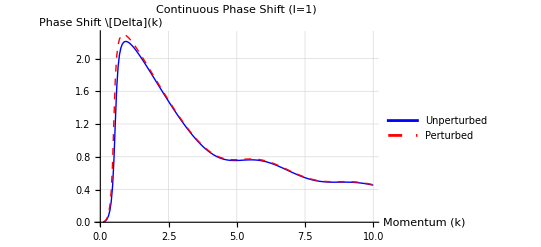

Exact Unperturbed Resonance k: 0.591228

Exact Perturbed Resonance k:   0.527948

Shift (\[Delta]k):               -0.0632794

-Graphics-

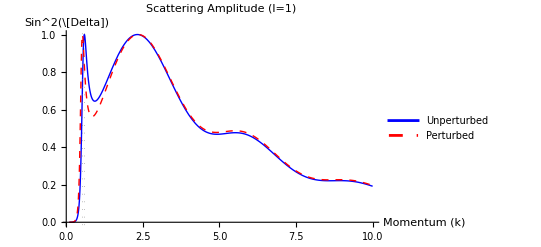

```mathematica
(*1. System Parameters*)
hbar=1;m=1;a=1;V0=9;lTarget=1; λ=0.2;

(*2. Define the Potentials*)
VUnperturbed[r_]:=If[r<a,-V0/(2m),0]
VPerturbed[r_]:=If[r<a,-(V0+λ*r)/(2m),0] (*0.5*r is the test shift*)

(*3. Phase Shift Function (now accepts MOMENTUM k)*)
PhaseShift[k_?NumericQ,l_Integer,pot_]:=Module[{E,Rmax,eps,eq,bc,solU,Rfun,gamma,jVal,yVal,jDeriv,yDeriv,num,den,delta},(*Calculate Energy from Momentum*)E=(hbar^2*k^2)/(2*m);
Rmax=2*a;
eps=10^-6;
eq=-(hbar^2/(2*m))*u''[r]+(pot[r]+(hbar^2*l*(l+1))/(2*m*r^2))*u[r]==E*u[r];
bc={u[eps]==eps^(l+1),u'[eps]==(l+1)*eps^l};
solU=NDSolveValue[{eq,bc},u,{r,eps,Rmax},Method->"StiffnessSwitching",MaxSteps->10000];
Rfun[r_]:=solU[r]/r;
gamma=Rfun'[Rmax]/Rfun[Rmax];
jVal=SphericalBesselJ[l,k*Rmax];
yVal=SphericalBesselY[l,k*Rmax];
jDeriv=k*(D[SphericalBesselJ[l,rho],rho]/. rho->k*Rmax);
yDeriv=k*(D[SphericalBesselY[l,rho],rho]/. rho->k*Rmax);
num=jDeriv-gamma*jVal;
     den=yDeriv-gamma*yVal;
delta=ArcTan[den,num];
Return[delta]]

(*Function to Unwrap and Normalize the Phase Array*)
UnwrapPhase[data_]:=Module[{unwrapped=data,diff,jump,tailShift},For[i=2,i<=Length[unwrapped],i++,diff=unwrapped[[i,2]]-unwrapped[[i-1,2]];
If[Abs[diff]>Pi/2,jump=Pi*Round[diff/Pi];
unwrapped[[i;;,2]]=unwrapped[[i;;,2]]-jump;];];
tailShift=-Pi*Round[Last[unwrapped][[2]]/Pi];
unwrapped[[All,2]]=unwrapped[[All,2]]+tailShift;
Return[unwrapped]]

(*2. Generate the Raw Data (in terms of k)*)
(*E=25 roughly corresponds to k=7.07,so we evaluate up to k=8.0*)
kRange=Range[0.1,10,0.05];
rawUnperturbedData=Table[{kV,PhaseShift[kV,lTarget,VUnperturbed]},{kV,kRange}];
rawPerturbedData=Table[{kV,PhaseShift[kV,lTarget,VPerturbed]},{kV,kRange}];

(*3. Clean the Data*)
smoothUnperturbedData=UnwrapPhase[rawUnperturbedData];
smoothPerturbedData=UnwrapPhase[rawPerturbedData];

(*4. Plot the Clean,Continuous Phase Shifts*)
ListLinePlot[{smoothUnperturbedData,smoothPerturbedData},AxesLabel->{"Momentum (k)","Phase Shift \\[Delta](k)"},PlotLabel->"Continuous Phase Shift (l="<>ToString[lTarget]<>")",PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}},PlotLegends->{"Unperturbed","Perturbed"},PlotRange->All,GridLines->Automatic]

(*5. Find the Resonances Numerically (in terms of k)*)
(*Convert old guessE=3.0 to k:sqrt(2*1*3.0)/1~2.45*)
guessK=0.5;

resKUnperturbed=kV/. FindRoot[Cos[PhaseShift[kV,lTarget,VUnperturbed]]==0,{kV,guessK}];
resKPerturbed=kV/. FindRoot[Cos[PhaseShift[kV,lTarget,VPerturbed]]==0,{kV,guessK}];

Print["Exact Unperturbed Resonance k: ",resKUnperturbed];
Print["Exact Perturbed Resonance k:   ",resKPerturbed];
Print["Shift (\\[Delta]k):               ",resKPerturbed-resKUnperturbed];

(*6. Plot the Overlay vs Momentum*)
AbsArgPlot[{Exp[2*I*PhaseShift[kV,lTarget,VUnperturbed]],Exp[2*I*PhaseShift[kV,lTarget,VPerturbed]]},{kV,0.1,10},AxesLabel->{"Momentum (k)","S Matrix"},PlotLabel->"Scattering Amplitude (l="<>ToString[lTarget]<>")",PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}},PlotLegends->{"Unperturbed","Perturbed"},PlotRange->All,PlotPoints->100,MaxRecursion->5,GridLines->{{resKUnperturbed,resKPerturbed},None},GridLinesStyle->Directive[Gray,Dotted]]
Plot[{Sin[PhaseShift[kV,lTarget,VUnperturbed]]^2,Sin[PhaseShift[kV,lTarget,VPerturbed]]^2},{kV,0.1,10},AxesLabel->{"Momentum (k)","Sin^2(\\[Delta])"},PlotLabel->"Scattering Amplitude (l="<>ToString[lTarget]<>")",PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}},PlotLegends->{"Unperturbed","Perturbed"},PlotRange->All,PlotPoints->100,MaxRecursion->5,GridLines->{{resKUnperturbed,resKPerturbed},None},GridLinesStyle->Directive[Gray,Dotted]]
```

```mathematica
V0test=9;
Kmom[u_]:=Sqrt[u^2+V0test]
PoleCondition[u_]:=u SphericalBesselJ[lTarget,Kmom[u]*a]SphericalHankelH1[lTarget-1,u*a]-Kmom[u] SphericalBesselJ[lTarget-1,Kmom[u]*a]SphericalHankelH1[lTarget,u*a]
NSolve[PoleCondition[z]==0 && 0<=Re[z]<10 && -5<Im[z]<1,{z}]
NSolve[PoleCondition[z]==0 && 0<=Re[z]<40&& -5<Im[z]<0,{z}];
(*ComplexPlot3D[1/PoleCondition[z],{z,-0.2-2I,6+0I}]*)
```

{{z→0.-3. ⅈ},{z→0.539202-0.0999098 ⅈ},{z→5.08598-1.5349 ⅈ},{z→8.62312-1.90916 ⅈ}}

```mathematica
Kmom[u_]:=Sqrt[u^2+V0]
J[p_,p_]:= a^3/2 (SphericalBesselJ[1,p*a]^2-SphericalBesselJ[0,p*a]*SphericalBesselJ[2,p*a]);
J[p_,q_]:= a^2/(p^2-q^2)(q SphericalBesselJ[1,p*a]*SphericalBesselJ[0,q*a]-p SphericalBesselJ[0,p*a]*SphericalBesselJ[1,q*a]);
Λ[u_]:=I*8*Pi^2*m*u/(1+I*2*V0*u*J[u,u]);
P1[u_]:=I/(u*a^2)(1/(Kmom[u]*SphericalBesselJ[0,Kmom[u]*a]*SphericalHankelH1[1,u*a]-u*SphericalBesselJ[1,Kmom[u]*a]*SphericalHankelH1[0,u*a]));
PsiUInside[r_,u_]:=P1[u]SphericalBesselJ[1,Kmom[u]*r]+SphericalBesselJ[1,u*r]
PsiUOutside[r_,u_]:=(PsiUInside[a,u]/SphericalHankelH1[1,u*a])SphericalHankelH1[1,u*r]

(* <Psi|Psi> for inner and outer parts *)
NormInsideNumerical[u_]:=NIntegrate[r^2*PsiUInside[r,u]^2,{r,0,a},Method->"LocalAdaptive"]
NormOutsideNumerical[u_]:=NIntegrate[r^2*PsiUOutside[r,u]^2,{r,a,Infinity},Method->"LocalAdaptive"]

(* d/dv<Psi|U(v)|psi> (only the seperable part of U depends on v)*)
(* Compute <v|V|psi> *)
overlap[v_?NumericQ,u_]:=(-V0/(2m))*Sqrt[2/Pi]*NIntegrate[r^2*PsiUInside[r,u]*SphericalBesselJ[1,v*r],{r,0,a},Method->"LocalAdaptive"]
(* Compute the seperable piece *)
matrixElement[v_?NumericQ,u_]:=Λ[v]*overlap[v,u]^2
(* Compute the derivative to give the norm *)
Needs["NumericalCalculus`"]
DerivativeNormNumerical[u_]:=(m/u)*ND[matrixElement[v,u],v,u]

(* Total Norm *)
TotalNormNumerical[u_?NumericQ]:=TotalNormNumerical[u]=NormInsideNumerical[u]+NormOutsideNumerical[u]-DerivativeNormNumerical[u]

PsiU[r_,u_]:=Piecewise[{{PsiUInside[r,u],r<a},{PsiUOutside[r,u],r>a}}];
PsiUNormalized[r_,u_]:=PsiU[r,u]/Sqrt[TotalNormNumerical[u]]

kres=0.5392022503575177-0.09990983772868195 ⅈ;
AbsArgPlot[PsiUNormalized[r,-kres],{r,0,3a}]
```

-Graphics-

```mathematica
NIntegrate[PsiU[r,-kres]^2,{r,0,Infinity}];
correction=NIntegrate[PsiU[r,-kres]^2*(-λ*r/(2m)),{r,0,Infinity}]/NIntegrate[PsiU[r,-kres]^2,{r,0,Infinity}]
correction1=NIntegrate[PsiUNormalized[r,-kres]^2*(-λ*r/(2m)),{r,0,Infinity}]
resKPerturbed-resKUnperturbed
```

-0.0798871+0.00969967 ⅈ

0.00050881+0.00706581 ⅈ

-0.0632794

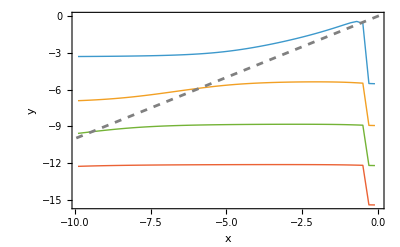

```mathematica
ncurves=4; (* Number of non 0 eigenvalue curves for a particular complex value*)

OrlovEigenvalues[uin_]:=Module[{uout},
uout=z/.NSolve[uin*SphericalBesselJ[lTarget,Kmom[z]*a]SphericalHankelH2[lTarget-1,uin*a]==Kmom[z] SphericalBesselJ[lTarget-1,Kmom[z]*a]SphericalHankelH2[lTarget,uin*a]&& -40<=Re[z]<=0.01 && -0.01<=Im[z]<40,{z}];
Return[uout]]
TakeLargest[Re[Select[OrlovEigenvalues[-1+2I],Re[#]<0&]],3];
uinRange=Range[-0.1,-10,-0.2];
RealOrlovEigenvaluesList[kim_,n_]:=ParallelTable[{k,TakeLargest[Re[Select[OrlovEigenvalues[k+kim*I],Re[#]<0&]],n]},{k,uinRange}];

EigenvalueCurves[kim_,n_]:=Table[Table[{pt[[1]],pt[[2,i]]},{pt,RealOrlovEigenvaluesList[kim,n]}],{i,n}]
Curves=EigenvalueCurves[0.09990983772868195,ncurves];

ListLinePlot[Curves,PlotStyle->Thick,(*Optional:makes curves easier to see*)PlotLayout->"Overlaid",Epilog->{(*45 degree line:y=x*)Directive[Dashed,Gray,Thickness[0.005]],InfiniteLine[{0,0},{1,1}]},PlotRange->All,Frame->True,FrameLabel->{"x","y"}]
```